# SKEO

## Slater-Koster LCAO tight-binding modeling with Evolutionary Optimization

### Load NC algebra library

Load noncommutative algebra library:

```mathematica
If[Length[PacletFind["NCAlgebra"]]==0,PacletInstall["https://github.com/NCAlgebra/NC/blob/master/NCAlgebra-6.0.3.paclet?raw=true"]];
<<NCAlgebra`;
SetNonCommutative[s,y,z,x,xy,yz,z2,xz,x2y2]; (*when caclulating SK elements orbitals should not be commutative*)
```

NCAlgebra::SmallCapSymbolsNonCommutative: All lower cap single letter symbols (e.g. a,b,c,...) were set as noncommutative.

### Load SKLE library

```mathematica
<<(NotebookDirectory[]<>"SKEO_lib.mx")
NCExpandFunc=NCExpand;(* from NCAlgebra lib *)
```

## TMDC monolayer

In this section we follow the model of  monolayers introduced in https://journals.aps.org/prb/abstract/10.1103/PhysRevB.97.085153

```mathematica
-Graphics-;
```

Now, let’s define basis orbitals (we are working in a basis of cubic harmonics: https://en.wikipedia.org/wiki/Cubic_harmonic)
Note that some of basis elements  (PE and PO representing chalcogenide dimer) are composed of orbitals localized on different lattice nodes.

## Basis definition

```mathematica
Dp2=1/(√2)(x2y2+I xy);(*even orbital at M*)
Dp1=-1/(√2)(xz+I yz);(*odd orbital at M*)
D0 = z2;(*even orbital at M*)
Dm1=1/(√2)(xz-I yz);(*odd orbital at M*)
Dm2=1/(√2)(x2y2-I xy);(*even orbital at M*)
PEp1={-1/2(x+I y),-1/2(x+I y)};(*even X2 dimer composed of up and down orbital*)
PE0 = {1/(√2)z,-1/(√2)z}; (*even X2 dimer composed of up and down orbital*)
PEm1={1/2(x-I y),1/2(x-I y)};(*even X2 dimer composed of up and down orbital*)
POp1={-1/2(x+I y),1/2(x+I y)};(*odd X2 dimer composed of up and down orbital*)
PO0 = {1/(√2)z,1/(√2)z};(*odd X2 dimer composed of up and down orbital*)
POm1={1/2(x-I y),1/2(-x+I y)};(*odd X2 dimer composed of up and down orbital*);
```

Collect all basis elements :

```mathematica
orbitals ={Dm2,D0,Dp2,PEm1,PE0,PEp1,Dm1,Dp1,POm1,PO0,POp1};
```

## Hoppings definition

Now define Matrix of hoppings for the each possible bond (we assume Next Nearest Neighbour approximation)

```mathematica
hopMM={{3/2 dr,(√3)/2 dr,0},{0,√3 dr,0},{-3/2 dr,(√3)/2 dr,0},{-3/2 dr,-(√3)/2 dr,0},{0,-√3 dr,0},{3/2 dr,-(√3)/2 dr,0}};
mxu = {{dr,0,dp},{-1/2 dr,(√3)/2 dr,dp},{-1/2 dr,-(√3)/2 dr,dp}};
xum = {{-dr,0,-dp},{1/2 dr,-(√3)/2 dr,-dp},{1/2 dr,(√3)/2 dr,-dp}};
mxd = {{dr,0,-dp},{-1/2 dr,(√3)/2 dr,-dp},{-1/2 dr,-(√3)/2 dr,-dp}};
xdm ={{-dr,0,dp},{1/2 dr,-(√3)/2 dr,dp},{1/2 dr,(√3)/2 dr,dp}};
hopMX={mxu,mxd,{1,2}}; 
hopXM={xum,xdm,{2,1}};(*last entry, {2,1}, means that hopping is from orbital combined of two nodes to single-noded*)
hopXX={hopMM,0,0,hopMM,{2,2}};(*0 means that we ommit given hopping; (2,2) means that we hop from dimer to dimer*);
```

Hoppings in our basis. Note that hoppings between dimers (consisting of orbitals at different nodes) are combined from multiple possibilities, with the option that some of them may be omitted (using “0” entry). In our case <up-element, down-element | up-element, down-element> element has 4 possible hoppings to be defined {<up,up>, <up,down>, <down|up>, <down|down>}. Here we decided to skip more distant mixed up-down and down-up hoppings.

```mathematica
Hop={
{hopMM,hopMM,hopMM,hopMX,hopMX,hopMX,0,0,0,0,0},
{hopMM,hopMM,hopMM,hopMX,hopMX,hopMX,0,0,0,0,0},
{hopMM,hopMM,hopMM,hopMX,hopMX,hopMX,0,0,0,0,0},
{hopXM,hopXM,hopXM,hopXX,hopXX,hopXX,0,0,0,0,0},
{hopXM,hopXM,hopXM,hopXX,hopXX,hopXX,0,0,0,0,0},
{hopXM,hopXM,hopXM,hopXX,hopXX,hopXX,0,0,0,0,0},
{0,0,0,0,0,0,hopMM,hopMM,hopMX,hopMX,hopMX},
{0,0,0,0,0,0,hopMM,hopMM,hopMX,hopMX,hopMX},
{0,0,0,0,0,0,hopXM,hopXM,hopXX,hopXX,hopXX},
{0,0,0,0,0,0,hopXM,hopXM,hopXX,hopXX,hopXX},
{0,0,0,0,0,0,hopXM,hopXM,hopXX,hopXX,hopXX}};
```

We also ommit hoppings between even and odd orbitals (zeros in Hop matrix) .

## Tests

### Single hoppings

```mathematica
GetHoppingSingle[D0,D0,x,y,z]
```

(3 z^2 (x^2/(x^2+y^2+z^2)+y^2/(x^2+y^2+z^2)) V_(d^2 π))/(x^2+y^2+z^2)+3/4 (x^2/(x^2+y^2+z^2)+y^2/(x^2+y^2+z^2))^2 V_(d^2 δ)+(z^2/(x^2+y^2+z^2)+1/2 (-x^2/(x^2+y^2+z^2)-y^2/(x^2+y^2+z^2)))^2 V_(d^2 σ)

```mathematica
FullSimplify[GetHopping[Dm1,POp1,{{{dr,0,dp}},{{dr,0,-dp}},{1,2}},True]/.{dp^2+dr^2->d^2}]
```

-(dp dr^2 ⅇ^(ⅈ dr kx) (2 V_(d p π)-√3 V_(d p σ)))/(√2 (d^2)^(3/2))

```mathematica
FullSimplify[GetHopping[Dm2,D0,{{3/2 dr,(√3)/2 dr,0}},True]]
```

((3 ⅈ+√3) ⅇ^(1/2 ⅈ dr (3 kx+√3 ky)) (V_(d^2 δ)-V_(d^2 σ)))/(8 √2)

### Matrix elements

```mathematica
H1v1=FullSimplify[GetHopping[D0,D0,hopMM,True]]
```

1/2 (Cos[√3 dr ky]+Cos[1/2 dr (3 kx-√3 ky)]+Cos[1/2 dr (3 kx+√3 ky)]) (3 V_(d^2 δ)+V_(d^2 σ))

```mathematica
FullSimplify[H1v1==1/2(3 Subscript[V, d^2 δ]+Subscript[V, d^2 σ])(2Cos[3/2 kx dr]*Cos[√3 /2 ky dr]+Cos[√3 ky dr])]
```

True

```mathematica
H1v2=FullSimplify[GetHopping[Dm2,D0,hopMM,True]]
```

1/4 √(3/2) (-2 Cos[√3 dr ky]+(1-ⅈ √3) Cos[1/2 dr (3 kx-√3 ky)]+(1+ⅈ √3) Cos[1/2 dr (3 kx+√3 ky)]) (V_(d^2 δ)-V_(d^2 σ))

```mathematica
FullSimplify[H1v2==(-√3)/(2 √2)(Subscript[V, d^2 σ]-Subscript[V, d^2 δ])(Cos[3/2 kx dr+√3/2 ky dr]Exp[I Pi/3]+Cos[3/2 kx dr-√3/2 ky dr]Exp[-I Pi/3]-Cos[√3 ky dr])]
```

True

```mathematica
H5v5=FullSimplify[GetHopping[PE0,PE0,hopXX,True]]
```

2 (Cos[√3 dr ky]+Cos[1/2 dr (3 kx-√3 ky)]+Cos[1/2 dr (3 kx+√3 ky)]) V_(p^2 π)

```mathematica
FullSimplify[H5v5==Subscript[V, p^2 π](4Cos[3/2 kx dr]*Cos[√3 /2 ky dr]+2Cos[√3 ky dr])]
```

True

```mathematica
H4v6=FullSimplify[GetHopping[PEm1,PEp1,hopXX,True]]
```

1/2 (-2 Cos[√3 dr ky]+(1-ⅈ √3) Cos[1/2 dr (3 kx-√3 ky)]+(1+ⅈ √3) Cos[1/2 dr (3 kx+√3 ky)]) (V_(p^2 π)-V_(p^2 σ))

```mathematica
FullSimplify[H4v6==(Subscript[V, p^2 σ]-Subscript[V, p^2 π])(Cos[3/2 kx dr+√3/2 ky dr]Exp[I Pi/3]+Cos[3/2 kx dr-√3/2 ky dr]Exp[-I Pi/3]-Cos[√3 ky dr])*(-1)]
```

True

```mathematica
H3v6=FullSimplify[GetHopping[Dp2,PEp1,hopMX,True]/.{dp^2+dr^2->d^2}]
```

1/(4 √2 (d^2)^(3/2))ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) (2 dr (-2 d^2+dr^2) (1-ⅈ √3+(1+ⅈ √3) ⅇ^(ⅈ √3 dr ky)-2 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p π)-dr^3 (-3 ⅈ+√3+(3 ⅈ+√3) ⅇ^(ⅈ √3 dr ky)-2 √3 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p σ))

```mathematica
FullSimplify[H3v6==dr/(√2 d)(√3/2 Subscript[V, d p σ](dp^2/d^2-1)-Subscript[V, d p π](dp^2/d^2+1))(Exp[I kx dr]+Exp[-I kx dr /2+I √3 ky dr/2-2I Pi /3]+Exp[-I kx dr /2-I √3 ky dr/2+2I Pi /3])*(-1)]
```

1/(√(d^2))d dr ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) (2 (-2 d^3+√(d^2) (d^2+dp^2)+d dr^2) (-1+ⅈ √3+(-1-ⅈ √3) ⅇ^(ⅈ √3 dr ky)+2 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p π)-((d^2)^(3/2)-√(d^2) dp^2-d dr^2) (-3 ⅈ+√3+(3 ⅈ+√3) ⅇ^(ⅈ √3 dr ky)-2 √3 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p σ))==0

```mathematica
H7v11=FullSimplify[GetHopping[Dm1,POp1,hopMX,True]/.{dp^2+dr^2->d^2}]
```

(dp dr^2 ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) (2 (1-ⅈ √3+(1+ⅈ √3) ⅇ^(ⅈ √3 dr ky)-2 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p π)-(-3 ⅈ+√3+(3 ⅈ+√3) ⅇ^(ⅈ √3 dr ky)-2 √3 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p σ)))/(2 √2 (d^2)^(3/2))

```mathematica
FullSimplify[H7v11==-(dp dr^2)/(√2 d^3)(√3 Subscript[V, d p σ]-2 Subscript[V, d p π])(Exp[I kx dr]+Exp[-I kx dr /2+I √3 ky dr/2-2I Pi/3]+Exp[-I kx dr /2-I √3 ky dr/2+2 I Pi/3])*(-1)]
```

1/(d √(d^2))(-d+√(d^2)) dp dr ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) ((-2+2 ⅈ √3+(-2-2 ⅈ √3) ⅇ^(ⅈ √3 dr ky)+4 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p π)+(-3 ⅈ+√3+(3 ⅈ+√3) ⅇ^(ⅈ √3 dr ky)-2 √3 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p σ))==0

```mathematica
H7v10=FullSimplify[GetHopping[Dm1,PO0,hopMX,True]/.{dp^2+dr^2->d^2}]
```

1/(2 (d^2)^(3/2))dr ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) ((d^2-2 dp^2) (1+ⅈ √3+(1-ⅈ √3) ⅇ^(ⅈ √3 dr ky)-2 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p π)+dp^2 (3 ⅈ+√3+(-3 ⅈ+√3) ⅇ^(ⅈ √3 dr ky)-2 √3 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p σ))

```mathematica
FullSimplify[H7v10==-dr/d(dp^2/d^2(√3 Subscript[V, d p σ]-2 Subscript[V, d p π])+Subscript[V, d p π])(Exp[I kx dr]+Exp[-I kx dr /2+I √3 ky dr/2+2I Pi/3]+Exp[-I kx dr /2-I √3 ky dr/2-2 I Pi/3])]
```

1/(√(d^2))d (-d+√(d^2)) dr ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) ((d^2-2 dp^2) (-1-ⅈ √3+ⅈ (ⅈ+√3) ⅇ^(ⅈ √3 dr ky)+2 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p π)-dp^2 (3 ⅈ+√3+(-3 ⅈ+√3) ⅇ^(ⅈ √3 dr ky)-2 √3 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p σ))==0

```mathematica
H8v9=FullSimplify[GetHopping[Dp1,POm1,hopMX,True]/.{dp^2+dr^2->d^2}]
```

(dp dr^2 ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) (2 (1+ⅈ √3+(1-ⅈ √3) ⅇ^(ⅈ √3 dr ky)-2 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p π)-(3 ⅈ+√3+(-3 ⅈ+√3) ⅇ^(ⅈ √3 dr ky)-2 √3 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p σ)))/(2 √2 (d^2)^(3/2))

```mathematica
FullSimplify[H8v9==(dp dr^2)/(√2 d^3)(√3 Subscript[V, d p σ]-2 Subscript[V, d p π])(Exp[I kx dr]+Exp[-I kx dr /2+I √3 ky dr/2+2I Pi/3]+Exp[-I kx dr /2-I √3 ky dr/2-2 I Pi/3])]
```

1/(d √(d^2))(-d+√(d^2)) dp dr ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) ((-2-2 ⅈ √3+2 ⅈ (ⅈ+√3) ⅇ^(ⅈ √3 dr ky)+4 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p π)+(3 ⅈ+√3+(-3 ⅈ+√3) ⅇ^(ⅈ √3 dr ky)-2 √3 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p σ))==0

```mathematica
H8v10=FullSimplify[GetHopping[Dp1,PO0,hopMX,True]/.{dp^2+dr^2->d^2}]
```

1/(2 (d^2)^(3/2))dr ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) ((d^2-2 dp^2) (-1+ⅈ √3+(-1-ⅈ √3) ⅇ^(ⅈ √3 dr ky)+2 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p π)-dp^2 (-3 ⅈ+√3+(3 ⅈ+√3) ⅇ^(ⅈ √3 dr ky)-2 √3 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p σ))

```mathematica
FullSimplify[H8v10==dr/d(dp^2/d^2(√3 Subscript[V, d p σ]-2 Subscript[V, d p π])+Subscript[V, d p π])(Exp[I kx dr]+Exp[-I kx dr /2+I √3 ky dr/2-2I Pi/3]+Exp[-I kx dr /2-I √3 ky dr/2+2 I Pi/3])]
```

1/(√(d^2))d (-d+√(d^2)) dr ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) ((d^2-2 dp^2) (-1+ⅈ √3+(-1-ⅈ √3) ⅇ^(ⅈ √3 dr ky)+2 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p π)-dp^2 (-3 ⅈ+√3+(3 ⅈ+√3) ⅇ^(ⅈ √3 dr ky)-2 √3 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) V_(d p σ))==0

```mathematica
H9v11=FullSimplify[GetHopping[POm1,POp1,hopXX,True]/.{dp^2+dr^2->d^2}]
```

1/2 (-2 Cos[√3 dr ky]+(1-ⅈ √3) Cos[1/2 dr (3 kx-√3 ky)]+(1+ⅈ √3) Cos[1/2 dr (3 kx+√3 ky)]) (V_(p^2 π)-V_(p^2 σ))

```mathematica
FullSimplify[H9v11==(Subscript[V, p^2 σ]-Subscript[V, p^2 π])(Cos[3/2 kx dr+√3/2 ky dr]Exp[I Pi/3]+Cos[3/2 kx dr-√3/2 ky dr]Exp[-I Pi/3]-Cos[√3 ky dr])*(-1)]
```

True

```mathematica
H9v10=FullSimplify[GetHopping[POm1,PO0,hopXX,True]/.{dp^2+dr^2->d^2}]
```

0

## TMDC heterostructure

In this section we introduce TB model for stacked TMDC heterostructure.

```mathematica
-Graphics-;
```

## Interalyer hoppings

```mathematica
-Graphics-;
```

Let' s define interalyer hoppings (intralayer are the same as in the previous chapter), <top layer | bottom layer>:

```mathematica
ihopMM=List[{-dr,0,-dzdd},{1/2 dr,-(√3)/2 dr,-dzdd},{1/2 dr,(√3)/2 dr,-dzdd}];
ihopMX={{{0,0,-dzdp}},0,{1,2}}; (* M from top layer only coupled with (nearer) up X-atom from bottom layer *)
ihopXM={0,{{0,0,-dzdp}},{2,1}}; (* only (nearer) down X-atom from top layer is coupled with M atom from bottom layer *)
ihopxx=List[{dr,0,-dzpp},{-1/2 dr,(√3)/2 dr,-dzpp},{-1/2 dr,-(√3)/2 dr,-dzpp}];
ihopXX={0,0,ihopxx,0,{2,2}};(* only down X-atom from top dimer is coupled with up X-atom from bottom dimer *)
```

```mathematica
IHop={
{ihopMM,ihopMM,ihopMM,ihopMX,ihopMX,ihopMX},
{ihopMM,ihopMM,ihopMM,ihopMX,ihopMX,ihopMX},
{ihopMM,ihopMM,ihopMM,ihopMX,ihopMX,ihopMX},
{ihopXM,ihopXM,ihopXM,ihopXX,ihopXX,ihopXX},
{ihopXM,ihopXM,ihopXM,ihopXX,ihopXX,ihopXX},
{ihopXM,ihopXM,ihopXM,ihopXX,ihopXX,ihopXX}};
```

```mathematica
Iorbitals ={Dm2,D0,Dp2,PEm1,PE0,PEp1};
```

```mathematica
HSKinter = HSKHoppings[Iorbitals,IHop,True];
```

[1,1]
(ⅇ^(-1/2 ⅈ dr (2 kx+√3 ky)) (ⅇ^((3 ⅈ dr kx)/2)+ⅇ^(1/2 ⅈ √3 dr ky)+ⅇ^(1/2 ⅈ dr (3 kx+2 √3 ky))) (4 (dr^4+2 dr^2 dzdd^2) V_(d^2 π)+(dr^4+8 dr^2 dzdd^2+8 dzdd^4) V_(d^2 δ)+3 dr^4 V_(d^2 σ)))/(8 (dr^2+dzdd^2)^2)

[1,2]
(√(3/2) dr^2 ⅇ^(-1/2 ⅈ dr (2 kx+√3 ky)) ((-1-ⅈ √3) ⅇ^((3 ⅈ dr kx)/2)+2 ⅇ^(1/2 ⅈ √3 dr ky)+ⅈ (ⅈ+√3) ⅇ^(1/2 ⅈ dr (3 kx+2 √3 ky))) (-4 dzdd^2 V_(d^2 π)+(dr^2+2 dzdd^2) V_(d^2 δ)-(dr^2-2 dzdd^2) V_(d^2 σ)))/(8 (dr^2+dzdd^2)^2)

[1,3]
(dr^4 ⅇ^(-1/2 ⅈ dr (2 kx+√3 ky)) ((1-ⅈ √3) ⅇ^((3 ⅈ dr kx)/2)-2 ⅇ^(1/2 ⅈ √3 dr ky)+(1+ⅈ √3) ⅇ^(1/2 ⅈ dr (3 kx+2 √3 ky))) (4 V_(d^2 π)-V_(d^2 δ)-3 V_(d^2 σ)))/(16 (dr^2+dzdd^2)^2)

[1,4]
0

[1,5]
0

[1,6]
0

[2,1]
(√(3/2) dr^2 ⅇ^(-1/2 ⅈ dr (2 kx+√3 ky)) (ⅈ (ⅈ+√3) ⅇ^((3 ⅈ dr kx)/2)+2 ⅇ^(1/2 ⅈ √3 dr ky)+(-1-ⅈ √3) ⅇ^(1/2 ⅈ dr (3 kx+2 √3 ky))) (-4 dzdd^2 V_(d^2 π)+(dr^2+2 dzdd^2) V_(d^2 δ)-(dr^2-2 dzdd^2) V_(d^2 σ)))/(8 (dr^2+dzdd^2)^2)

[2,2]
(ⅇ^(-1/2 ⅈ dr (2 kx+√3 ky)) (ⅇ^((3 ⅈ dr kx)/2)+ⅇ^(1/2 ⅈ √3 dr ky)+ⅇ^(1/2 ⅈ dr (3 kx+2 √3 ky))) (12 dr^2 dzdd^2 V_(d^2 π)+3 dr^4 V_(d^2 δ)+(dr^2-2 dzdd^2)^2 V_(d^2 σ)))/(4 (dr^2+dzdd^2)^2)

[2,3]
(√(3/2) dr^2 ⅇ^(-1/2 ⅈ dr (2 kx+√3 ky)) ((-1-ⅈ √3) ⅇ^((3 ⅈ dr kx)/2)+2 ⅇ^(1/2 ⅈ √3 dr ky)+ⅈ (ⅈ+√3) ⅇ^(1/2 ⅈ dr (3 kx+2 √3 ky))) (-4 dzdd^2 V_(d^2 π)+(dr^2+2 dzdd^2) V_(d^2 δ)-(dr^2-2 dzdd^2) V_(d^2 σ)))/(8 (dr^2+dzdd^2)^2)

[2,4]
0

[2,5]
(dzdp V_(d p σ))/(√2 √(dzdp^2))

[2,6]
0

[3,1]
(dr^4 ⅇ^(-1/2 ⅈ dr (2 kx+√3 ky)) ((1+ⅈ √3) ⅇ^((3 ⅈ dr kx)/2)-2 ⅇ^(1/2 ⅈ √3 dr ky)+(1-ⅈ √3) ⅇ^(1/2 ⅈ dr (3 kx+2 √3 ky))) (4 V_(d^2 π)-V_(d^2 δ)-3 V_(d^2 σ)))/(16 (dr^2+dzdd^2)^2)

[3,2]
(√(3/2) dr^2 ⅇ^(-1/2 ⅈ dr (2 kx+√3 ky)) (ⅈ (ⅈ+√3) ⅇ^((3 ⅈ dr kx)/2)+2 ⅇ^(1/2 ⅈ √3 dr ky)+(-1-ⅈ √3) ⅇ^(1/2 ⅈ dr (3 kx+2 √3 ky))) (-4 dzdd^2 V_(d^2 π)+(dr^2+2 dzdd^2) V_(d^2 δ)-(dr^2-2 dzdd^2) V_(d^2 σ)))/(8 (dr^2+dzdd^2)^2)

[3,3]
(ⅇ^(-1/2 ⅈ dr (2 kx+√3 ky)) (ⅇ^((3 ⅈ dr kx)/2)+ⅇ^(1/2 ⅈ √3 dr ky)+ⅇ^(1/2 ⅈ dr (3 kx+2 √3 ky))) (4 (dr^4+2 dr^2 dzdd^2) V_(d^2 π)+(dr^4+8 dr^2 dzdd^2+8 dzdd^4) V_(d^2 δ)+3 dr^4 V_(d^2 σ)))/(8 (dr^2+dzdd^2)^2)

[3,4]
0

[3,5]
0

[3,6]
0

[4,1]
0

[4,2]
0

[4,3]
0

[4,4]
(ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) (1+ⅇ^(ⅈ √3 dr ky)+ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) ((dr^2+2 dzpp^2) V_(p^2 π)+dr^2 V_(p^2 σ)))/(4 (dr^2+dzpp^2))

[4,5]
(dr dzpp ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) (-1-ⅈ √3+ⅈ (ⅈ+√3) ⅇ^(ⅈ √3 dr ky)+2 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) (V_(p^2 π)-V_(p^2 σ)))/(4 √2 (dr^2+dzpp^2))

[4,6]
(dr^2 ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) (-1+ⅈ √3+(-1-ⅈ √3) ⅇ^(ⅈ √3 dr ky)+2 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) (V_(p^2 π)-V_(p^2 σ)))/(8 (dr^2+dzpp^2))

[5,1]
0

[5,2]
(dzdp V_(d p σ))/(√2 √(dzdp^2))

[5,3]
0

[5,4]
(dr dzpp ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) (1-ⅈ √3+(1+ⅈ √3) ⅇ^(ⅈ √3 dr ky)-2 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) (V_(p^2 π)-V_(p^2 σ)))/(4 √2 (dr^2+dzpp^2))

[5,5]
-(ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) (1+ⅇ^(ⅈ √3 dr ky)+ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) (dr^2 V_(p^2 π)+dzpp^2 V_(p^2 σ)))/(2 (dr^2+dzpp^2))

[5,6]
(dr dzpp ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) (-1-ⅈ √3+ⅈ (ⅈ+√3) ⅇ^(ⅈ √3 dr ky)+2 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) (V_(p^2 π)-V_(p^2 σ)))/(4 √2 (dr^2+dzpp^2))

[6,1]
0

[6,2]
0

[6,3]
0

[6,4]
(dr^2 ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) (-1-ⅈ √3+ⅈ (ⅈ+√3) ⅇ^(ⅈ √3 dr ky)+2 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) (V_(p^2 π)-V_(p^2 σ)))/(8 (dr^2+dzpp^2))

[6,5]
(dr dzpp ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) (1-ⅈ √3+(1+ⅈ √3) ⅇ^(ⅈ √3 dr ky)-2 ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) (V_(p^2 π)-V_(p^2 σ)))/(4 √2 (dr^2+dzpp^2))

[6,6]
(ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) (1+ⅇ^(ⅈ √3 dr ky)+ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) ((dr^2+2 dzpp^2) V_(p^2 π)+dr^2 V_(p^2 σ)))/(4 (dr^2+dzpp^2))

```mathematica
HSKinter[[2,2]](*D0-D0*)
```

(ⅇ^(-1/2 ⅈ dr (2 kx+√3 ky)) (ⅇ^((3 ⅈ dr kx)/2)+ⅇ^(1/2 ⅈ √3 dr ky)+ⅇ^(1/2 ⅈ dr (3 kx+2 √3 ky))) (12 dr^2 dzdd^2 V_(d^2 π)+3 dr^4 V_(d^2 δ)+(dr^2-2 dzdd^2)^2 V_(d^2 σ)))/(4 (dr^2+dzdd^2)^2)

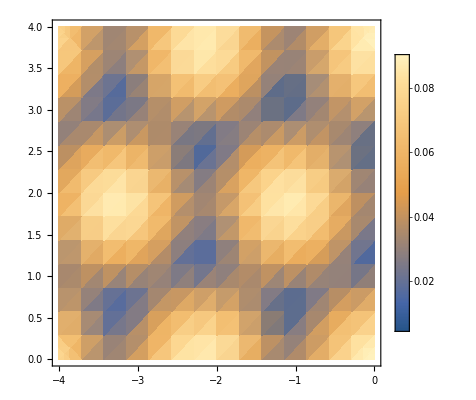

```mathematica
DensityPlot[Abs[HSKinter[[2,2]]/.{dr->3.323/√3,dzpp->3.05, dzdd->6.4, Subscript[V, d^2 π]-> 1.8318,Subscript[V, d^2 δ]->-0.3299,Subscript[V, d^2 σ]->-0.5,Subscript[V, p^2 π]->-0.1547,Subscript[V, p^2 σ]->-1.1006}],{kx,-4,0},{ky,0,4},PlotLegends->Automatic]
```

```mathematica
HSKinter[[5,5]](*P0-P0*)
```

-(ⅇ^(-1/2 ⅈ dr (kx+√3 ky)) (1+ⅇ^(ⅈ √3 dr ky)+ⅇ^(1/2 ⅈ dr (3 kx+√3 ky))) (dr^2 V_(p^2 π)+dzpp^2 V_(p^2 σ)))/(2 (dr^2+dzpp^2))

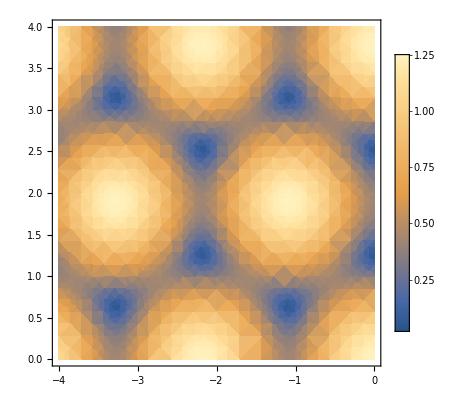

```mathematica
DensityPlot[Abs[HSKinter[[5,5]]/.{dr->3.323/√3,dzpp->3.05, dzdd->6.4, Subscript[V, d^2 π]-> 1.8318,Subscript[V, d^2 δ]->-0.3299,Subscript[V, d^2 σ]->-0.5,Subscript[V, p^2 π]->-0.1547,Subscript[V, p^2 σ]->-1.1006}],{kx,-4,0},{ky,0,4},PlotLegends->Automatic]
```

```mathematica
Abs[HSKinter[[2,5]]/.{dr->3.323/√3,dzpp->3.05, dzdd->6.4, dzdp->4.5,Subscript[V, d^2 π]-> 1.8318,Subscript[V, d^2 δ]->-0.3299,Subscript[V, d^2 σ]->-0.5,Subscript[V, p^2 π]->-0.1547,Subscript[V, p^2 σ]->-1.1006}]
```

0.707107 Abs[V_(d p σ)]

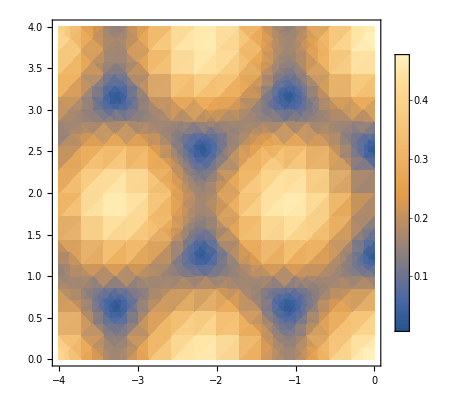

```mathematica
DensityPlot[Abs[HSKinter[[1,1]]/.{dr->3.323/√3,dzpp->3.05, dzdd->6.4, Subscript[V, d^2 π]-> 1.8318,Subscript[V, d^2 δ]->-0.3299,Subscript[V, d^2 σ]->-0.5,Subscript[V, p^2 π]->-0.1547,Subscript[V, p^2 σ]->-1.1006}],{kx,-4,0},{ky,0,4},PlotLegends->Automatic]
```